# The Massive Scalar Casimir effect for Degenerate Vacua

This Mathematica notebook serves as a companion to the article ArXiV: XXXX.XXXX containing all calculations and plots.

## Figures

### Potential-xi

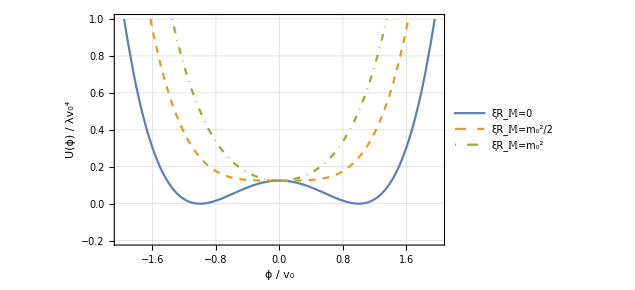

```mathematica
U[ϕ_,λ_,v_,ξR_]:=λ/8(ϕ^2-v^2)^2+1/2 ξR ϕ^2
Plot[{U[ϕ,1,1,0],U[ϕ,1,1,1/2],U[ϕ,1,1,1]},{ϕ,-2,2},Frame->True,GridLines->Automatic,GridLinesStyle->Dotted,PlotStyle->{,Dashed,DotDashed},PlotRange->{-0.2,1},ImageSize->470,FrameLabel->{Style["ϕ / v_0",20],Style["U(ϕ) / λv_0^4",20]},Method->{"AxesInFront"->False},PlotLegends->Placed[LineLegend[{"ξR_𝕄=0","ξR_𝕄=m_0^2/2","ξR_𝕄=m_0^2"},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&)],{0.5,0.76}]]
```

### Effective potential

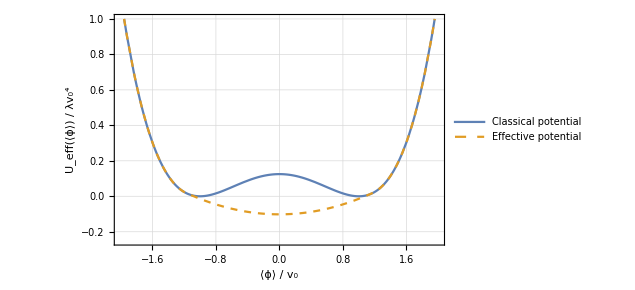

```mathematica
U[x_]:=1/8(x^2-1)^2
Eff[x_]:=Piecewise[{{U[x],Abs[x]>1.2},{1/8(0.7 x^2-0.8144),Abs[x]≤1.2}}]
Plot[{U[x],Eff[x]},{x,-2,2},Frame->True,GridLines->Automatic,GridLinesStyle->Dotted,PlotStyle->{,Dashed},PlotRange->{-0.25,1},ImageSize->470,FrameLabel->{Style["⟨ϕ⟩ / v_0",20],Style["U_eff(⟨ϕ⟩) / λv_0^4",20]},PlotLegends->Placed[LineLegend[{"Classical potential","Effective potential"},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&)],{0.7,0.75}]]
```

### Saddle points

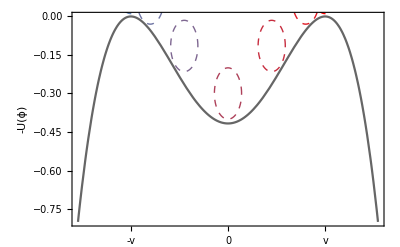

-Graphics-

```mathematica
Plot[-λ/24 (ϕ^2-v^2)^2/.{λ->10,v->1},{ϕ,-1.6,1.6},Frame->True,FrameLabel->{,Style["-U(ϕ)",20]},PlotRange->{0.7,-0.8},FrameTicks->{{None,None},{{{-1,Style["-v",20]},{0,Style[0,20]},{1,Style["v",20]}},None}},
Epilog->{
{ColorData[97,1],Dashed,Thickness->0.007,{Circle[{-1,0.111},{0.14,0.1}]}},
{Blend[{Red,ColorData[97,1]},0.9],Dashed,Thickness->0.007,{Circle[{-0.8,0.07},{0.14,0.1}]}},
{Blend[{Red,ColorData[97,1]},0.8],Dashed,Thickness->0.007,{Circle[{-0.45,-0.115},{0.14,0.1}]}},
{Blend[{Red,ColorData[97,1]},0.5],Dashed,Thickness->0.007,{Circle[{0,-0.3},{0.14,0.1}]}},
{Blend[{Red,ColorData[97,1]},0.2],Dashed,Thickness->0.007,{Circle[{0.8,0.07},{0.14,0.1}]}},
{Blend[{Red,ColorData[97,1]},0.35],Dashed,Thickness->0.007,{Circle[{0.45,-0.115},{0.14,0.1}]}},
{Red,Dashed,Thickness->0.007,{Circle[{1,0.111},{0.14,0.1}]}},
{ColorData[97,1],PointSize-> 0.092,Point[{-1,0.11}]},
{Red,PointSize-> 0.092,Point[{1,0.11}]}
},
PlotStyle->{Black,Opacity[0.6]}]
Show[
Plot[-10,{τ,-5,5},Frame->True,PlotRange->{1.5,-1.5},FrameLabel->{,Style["ϕ_i(τ)",20]},FrameTicks->{{{{1,Style["v",20]},{0,Style["0",20]},{-1,Style["-v",20]}},None},{{{-5,Style["0",20]},{0,Style["τ_0",20]},{5,Style["β",20]}},None}}],
Plot[Tanh[4τ],{τ,-5,5},ColorFunction->Function[{x,y},Opacity[2y,Red]],PlotStyle->Dashed],
Plot[Tanh[4τ],{τ,-5,5},ColorFunction->Function[{x,y},Opacity[(1-y),ColorData[97,1]]],PlotStyle->Dashed],
Plot[-1,{τ,-5,5},PlotStyle->{Opacity[0.5]}],
Plot[1,{τ,-5,5},PlotStyle->{Red,Opacity[0.5]}]
]
```

## Tunneling

Initialisation cell for tunneling expressions (ctrl+8)

```mathematica
meff[m_,ξ_,R_]:=Piecewise[{{√(m^2-2ξ R),m^2-2ξ R≥0}},]
veff[λ_,v_,ξ_,R_]:=Piecewise[{{√(v^2-(2ξ R)/λ),v^2-(2ξ R)/λ≥0}},]
RhoTun[V_,λ_,v_]:=-2v √((√λ v^3)/(V π))ⅇ^((-2 √λ v^3 V)/3)
PTun[V_,λ_,v_]:=(λ^(3/4)v^4 ⅇ^(-(2 √λ v^3 V)/(3 λ)) (-4 √λ v^3 V+3 ))/(3 √π √(v^3 V))
```

## Torus

Here we plot the degenerate vacua Casimir energy for toroidal geometries

### T^1

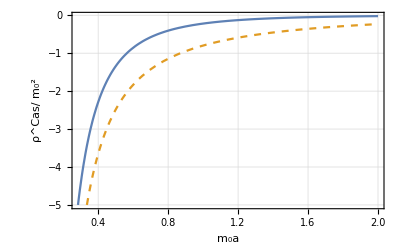

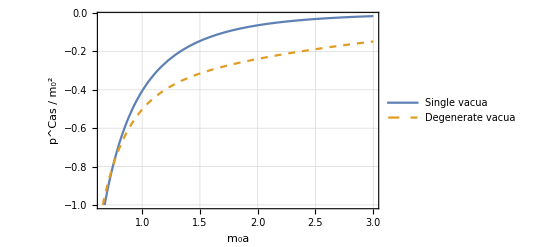

```mathematica
VT1[a_]:=a
RhoT1[a_,m_]:=NIntegrate[-m^2/π(√(t^2-1))/(ⅇ^(m a t)-1),{t,1,∞}]
PT1[a_,m_]:=NIntegrate[-(m^2 √(-1+t^2) (1+ⅇ^(a m t) (-1+a m t)))/((-1+ⅇ^(a m t))^2 π),{t,1,∞}]
Plot[{RhoT1[a,1],RhoT1[a,1]+RhoTun[VT1[a],1,1]},{a,0,2},PlotStyle->{,Dashed},PlotRange->{0,-5},Frame->True,FrameLabel->{Style["m_0a",20],Style["ρ^Cas/ m_0^2",20]},GridLines->Automatic,GridLinesStyle->Dotted]
Plot[{PT1[a,1],PT1[a,1]+PTun[VT1[a],1,1]},{a,0,3},PlotStyle->{,Dashed},Frame->True,FrameLabel->{Style["m_0a",20],Style["p^Cas / m_0^2",20]},PlotRange->{0,-1},GridLines->Automatic,GridLinesStyle->Dotted,PlotLegends->Placed[LineLegend[{"Single vacua","Degenerate vacua"},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&)],{0.7,0.35}]]
```

### T^2

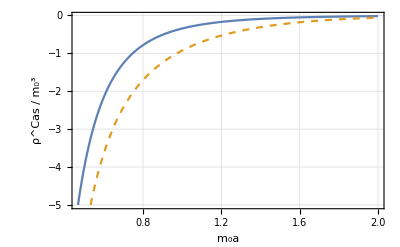

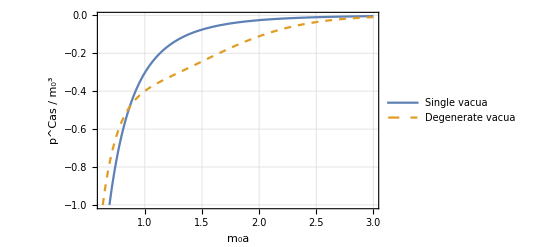

```mathematica
VT2[a_]:=a^2
RhoT2[a_,m_]:=-m^3/(4π)NIntegrate[(t^2-1)/(ⅇ^(m a t)-1),{t,1,∞}]-m^2/(π a)NIntegrate[(√(t^2-1))/(ⅇ^(m a t)-1),{t,1,∞}]
PT2[a_,m_]:=NIntegrate[-(m^3 (-1+t^2) (2+ⅇ^(a m t) (-2+a m t)))/(8 (-1+ⅇ^(a m t))^2 π),{t,1,∞}]+NIntegrate[-(m^2 √(-1+t^2) (1+ⅇ^(a m t) (-1+a m t)))/(2 a (-1+ⅇ^(a m t))^2 π),{t,1,∞}]
Plot[{RhoT2[a,1],RhoT2[a,1]+RhoTun[VT2[a],1,1]},{a,0,2},PlotRange->{0,-5},Frame->True,FrameLabel->{Style["m_0a",20],Style["ρ^Cas / m_0^3",20]},PlotStyle->{,Dashed},GridLines->Automatic,GridLinesStyle->Dotted]
Plot[{PT2[a,1],PT2[a,1]+PTun[VT2[a],1,1]},{a,0,3},PlotRange->{0,-1},PlotStyle->{,Dashed},Frame->True,FrameLabel->{Style["m_0a",20],Style["p^Cas / m_0^3",20]},GridLines->Automatic,GridLinesStyle->Dotted,PlotLegends->Placed[LineLegend[{"Single vacua","Degenerate vacua"},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&)],{0.7,0.35}]]
```

### T^3

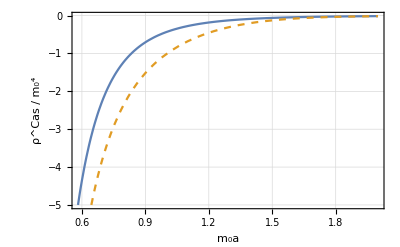

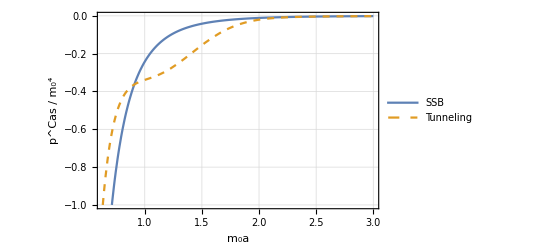

```mathematica
VT3[a_]:=a^3
RhoT3[a_,m_]:=-m^4/(6 π^2)NIntegrate[((t^2-1)^(3/2))/(ⅇ^(m a t)-1),{t,1,∞}]-m^3/(4π a)NIntegrate[(t^2-1)/(ⅇ^(m a t)-1),{t,1,∞}]-m^2/(π a^2)NIntegrate[(√(t^2-1))/(ⅇ^(m a t)-1),{t,1,∞}]
PT3[a_,m_]:=NIntegrate[-(m^4 (-1+t^2)^(3/2) (3+ⅇ^(a m t) (-3+a m t)))/(18 (-1+ⅇ^(a m t))^2 π^2),{t,1,∞}]+NIntegrate[-(m^3 (-1+t^2) (2+ⅇ^(a m t) (-2+a m t)))/(12 a (-1+ⅇ^(a m t))^2 π),{t,1,∞}]+NIntegrate[-(m^2 √(-1+t^2) (1+ⅇ^(a m t) (-1+a m t)))/(3 a^2 (-1+ⅇ^(a m t))^2 π),{t,1,∞}]
Plot[{RhoT3[a,1],RhoT3[a,1]+RhoTun[VT3[a],1,1]},{a,0,2},PlotRange->{0,-5},Frame->True,FrameLabel->{Style["m_0a",20],Style["ρ^Cas / m_0^4",20]},PlotStyle->{,Dashed},GridLines->Automatic,GridLinesStyle->Dotted]
Plot[{PT3[a,1],PT3[a,1]+PTun[VT3[a],1,1]},{a,0,3},PlotRange->{0,-1},PlotStyle->{,Dashed},Frame->True,FrameLabel->{Style["m_0a",20],Style["p^Cas / m_0^4",20]},GridLines->Automatic,GridLinesStyle->Dotted,PlotLegends->Placed[LineLegend[{"SSB","Tunneling"},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&)],{0.7,0.35}]]
```

## Sphere

Here we plot the degenerate vacua Casimir energy for spherical geometries

### S^2

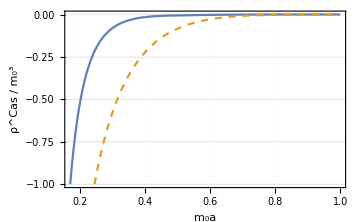
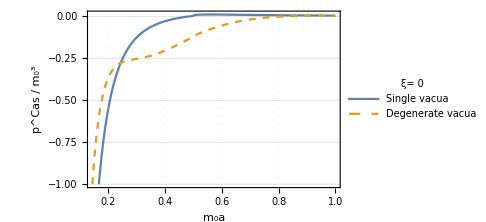
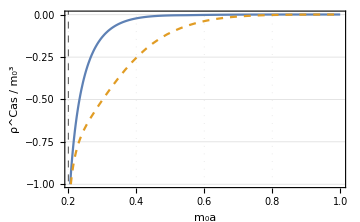
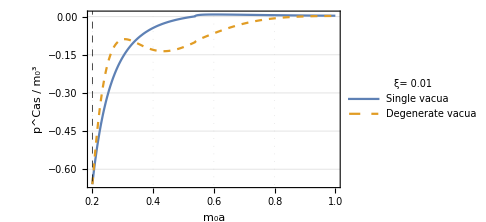
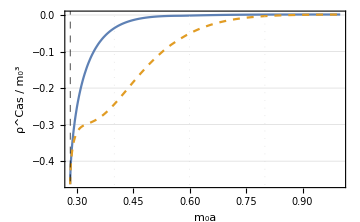
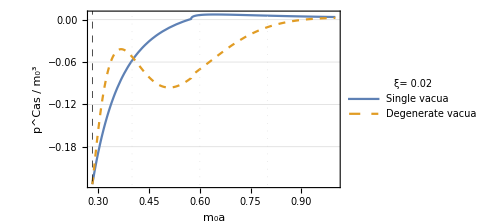
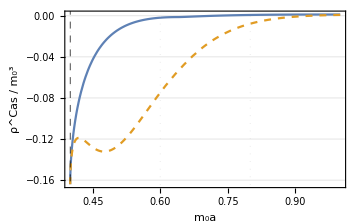
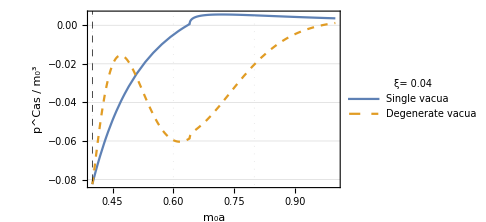

{{,}}

```mathematica
VS2[a_]:=4π a^2
RS2[a_]:=2/a^2
RhoS2[a_,m_?NumericQ]:=Piecewise[{{NIntegrate[((m^2 a^2-1/4)^(3/2))/(2π a^3) (t √(1-t^2))/(ⅇ^(2π t √(m^2 a^2-1/4))+1),{t,0,1}],m^2 a^2-1/4≥0},{NIntegrate[-((1/4-m^2 a^2)^(3/2))/(4π a^3) t √(1-t^2)Tan[π t √(1/4-m^2 a^2)],{t,0,1}],m^2 a^2-1/4<0}}]-m^3/(24 π)1/(4π a^2)
PS2[a_,m_?NumericQ]:=RhoS2[a,m]/2+m^3/(24 π)1/(4π a^2)+Piecewise[{{NIntegrate[(m^2(m^2 a^2-1/4)^(1/2))/(4π a) t/(√(1-t^2)(ⅇ^(2π t √(m^2 a^2-1/4))+1)),{t,0,1}],m^2 a^2-1/4≥0},{NIntegrate[-(m^2(1/4-m^2 a^2)^(1/2))/(8π a) t/(√(1-t^2))Tan[π t √(1/4-m^2 a^2)],{t,0,1}],m^2 a^2-1/4<0}}]
PlotRhoS2[ξ_]:=Plot[{RhoS2[a,meff[1,ξ,RS2[a]]],RhoS2[a,meff[1,ξ,RS2[a]]]+RhoTun[VS2[a],1,veff[1,1,ξ,RS2[a]]]},{a,0,1},PlotRange->{{0,1},{0.03,-1}},Frame->True,FrameLabel->{Style["m_0a",20],Style["ρ^Cas / m_0^3",20]},PlotStyle->{,Dashed},GridLines->{{0.2,0.4,0.6,0.8,{√(4ξ),Directive[Dashed,Black]}},Automatic},GridLinesStyle->Dotted,ImageSize->Medium]
PlotPS2[ξ_]:=Plot[{PS2[a,meff[1,ξ,RS2[a]]],PS2[a,meff[1,ξ,RS2[a]]]+PTun[VS2[a],1,veff[1,1,ξ,RS2[a]]]},{a,0,1},PlotRange->{{0,1},{0.03,-1}},Frame->True,FrameLabel->{Style["m_0a",20],Style["p^Cas / m_0^3",20]},PlotStyle->{,Dashed},GridLines->{{0.2,0.4,0.6,0.8,{√(4ξ),Directive[Dashed,Black]}},Automatic},GridLinesStyle->Dotted,PlotLegends->Placed[LineLegend[{"Single vacua","Degenerate vacua"},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&),LegendLabel->StringForm["ξ= ``",ξ]],{0.7,0.35}],ImageSize->Medium]
{{PlotRhoS2[0], PlotPS2[0]}, {PlotRhoS2[0.01], PlotPS2[0.01]}, {PlotRhoS2[0.02], PlotPS2[0.02]}, {PlotRhoS2[0.04], PlotPS2[0.04]}}
{{Manipulate[PlotRhoS2[ξ],{{ξ,0},0,1/6}], Manipulate[PlotPS2[ξ],{{ξ,0},0,1/6}]}}
```

### S^3

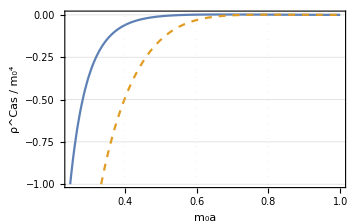
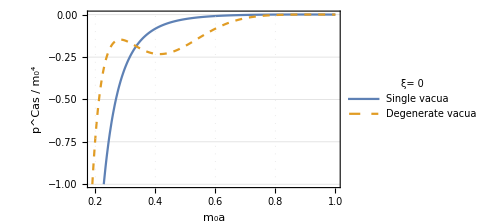
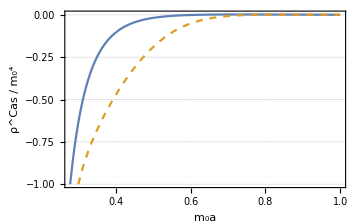
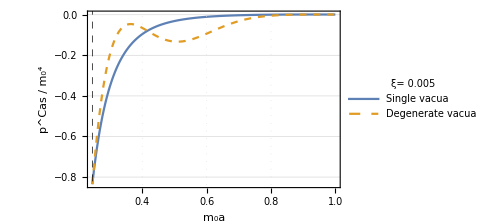
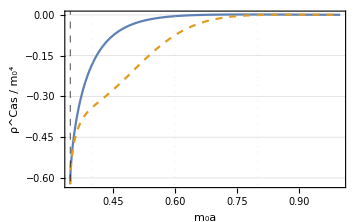
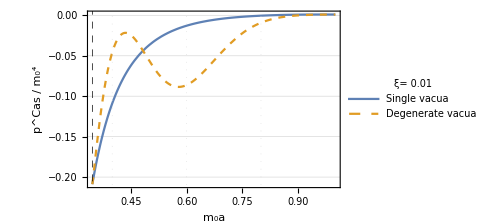
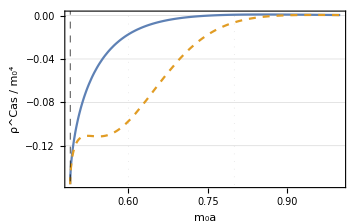
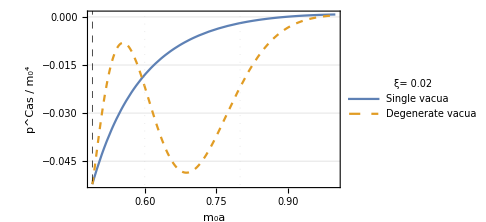

{{,}}

```mathematica
VS3[a_]:=2 π^2 a^3
RS3[a_]:=6/a^2
RhoS3[a_,ξ_,m_?NumericQ]:=Piecewise[{{NIntegrate[((m^2 a^2+6ξ-1)^2)/(2 π^2 a^4) (t^2 √(t^2-1))/(ⅇ^(2π t √(m^2 a^2+6ξ-1))-1),{t,1,∞}],m^2 a^2+6ξ-1≥0},{NIntegrate[((1-6ξ-m^2 a^2)^2)/(2 π^2 a^4) (t^2 √(t^2+1))/(ⅇ^(2π t √(1-6ξ-m^2 a^2))-1),{t,0,∞}]+NIntegrate[((1-6ξ-m^2 a^2)^2)/(4 π^2 a^4) t^2 √(1-t^2)Cot[π t √(1-6ξ-m^2 a^2)],{t,0,1}],m^2 a^2+6ξ-1<0}}]
PS3[a_,ξ_,m_?NumericQ]:=RhoS3[a,ξ,m]/3+Piecewise[{{NIntegrate[(m^2(m^2 a^2+6ξ-1))/(6 π^2 a^2) t^2/(√(t^2-1)(ⅇ^(2π t √(m^2 a^2+6ξ-1))-1)),{t,1,∞}],m^2 a^2+6ξ-1≥0},{NIntegrate[(m^2(1-6ξ-m^2 a^2))/(6 π^2 a^2) t^2/(√(t^2+1)(ⅇ^(2π t √(1-6ξ-m^2 a^2))-1)),{t,0,∞}]+NIntegrate[(m^2(1-6ξ-m^2 a^2))/(12 π^2 a^2) t^2/(√(1-t^2))Cot[π t √(1-6ξ-m^2 a^2)],{t,0,1}],m^2 a^2+6ξ-1<0}}]
PlotRhoS3[ξ_]:=Plot[{RhoS3[a,0,meff[1,ξ,RS3[a]]],RhoS3[a,0,meff[1,ξ,RS3[a]]]+RhoTun[VS3[a],1,veff[1,1,ξ,RS3[a]]]},{a,0,1},PlotRange->{{0,1},{0.03,-1}},Frame->True,FrameLabel->{Style["m_0a",20],Style["ρ^Cas / m_0^4",20]},PlotStyle->{,Dashed},GridLines->{{0.2,0.4,0.6,0.8,{√(12ξ),Directive[Dashed,Black]}},Automatic},GridLinesStyle->Dotted,ImageSize->Medium]
PlotPS3[ξ_]:=Plot[{PS3[a,0,meff[1,ξ,RS3[a]]],PS3[a,0,meff[1,ξ,RS3[a]]]+PTun[VS3[a],1,veff[1,1,ξ,RS3[a]]]},{a,0,1},PlotRange->{{0,1},{0.03,-1}},Frame->True,FrameLabel->{Style["m_0a",20],Style["p^Cas / m_0^4",20]},PlotStyle->{,Dashed},GridLines->{{0.2,0.4,0.6,0.8,{√(12ξ),Directive[Dashed,Black]}},Automatic},GridLinesStyle->Dotted,PlotLegends->Placed[LineLegend[{"Single vacua","Degenerate vacua"},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&),LegendLabel->StringForm["ξ= ``",ξ]],{0.7,0.35}],ImageSize->Medium]
{{PlotRhoS3[0], PlotPS3[0]}, {PlotRhoS3[0.005], PlotPS3[0.005]}, {PlotRhoS3[0.01], PlotPS3[0.01]}, {PlotRhoS3[0.02], PlotPS3[0.02]}}
{{Manipulate[PlotRhoS3[ξ],{{ξ,0},0,1/6}], Manipulate[PlotPS3[ξ],{{ξ,0},0,1/6}]}}
```